## DIRK - Diagonally Implicit Runge–Kutta methods

Francesco Torsello

References
[1] J. C. Butcher, Numerical Methods for Ordinary Differential Equations, John Wiley & Sons, 2008, ISBN: 9780470753750
[2] Kennedy, Christopher A., Carpenter, Mark H., NASA, Diagonally Implicit Runge-Kutta Methods for Ordinary Differential Equations. A Review. https://ntrs.nasa.gov/archive/nasa/casi.ntrs.nasa.gov/20160005923.pdf
[3] Stål, Josefine, Implementation of Singly Diagonally Implicit Runge-Kutta Methods with Constant Step Sizes, Bachelor’s Theses in Mathematical Sciences, 2015, ISSN: 1654-6229, http://lup.lub.lu.se/student-papers/record/7851608

[4] A. Kværnø, S.P. Nørsett, B. Owren, Runge-Kutta research in Trondheim, Applied Numerical Mathematics, Volume 22, Issues 1–3, 1996, pp. 263-277, ISSN 0168-9274, https://doi.org/10.1016/S0168-9274(96)00037-2

[5] Kværnø, Singly Diagonally Implicit Runge–Kutta Methods with an Explicit First Stage, A.BIT Numerical Mathematics (2004) 44 : 489. https : // doi.org/10.1023/B : BITN .0000046811 .70614 .38

Useful links
[6] https://en.wikipedia.org/wiki/List_of_Runge % E2 %80 %93 Kutta_methods

### Introduction

From [1],

-Graphics-

and from the introduction of [2],

-Graphics-

-Graphics-

### Utility functions

```mathematica
Clear[timed];
SetAttributes[timed,HoldAll]
timed[expr_]:=With[{start=AbsoluteTime[]},
Block[{},
PrintTemporary["Elapsed time = "Dynamic[AbsoluteTime[]-start,UpdateInterval->.1]];
expr
];
Print["Elapsed time = "<>ToString[AbsoluteTime[]-start]];
]
```

### The chosen DIRK method

We take the following two excerpts from [4],

-Graphics-

-Graphics-

#### ESDIRK 3/2 with s=4 stages, L-stable, embedded (but there is no adaptive time step implemented in this notebook)

The implemented ESDIRK method is taken from [5, p.497]. Defining the vectors c

```mathematica
c={{0},{2γ},{1},{1}};
```

```mathematica
A={
{0,0,0,0},
{γ,γ,0,0},
{(-4 γ^2+6γ-1)/(4γ),(-2γ+1)/(4γ),γ,0},
{(6γ-1)/(12γ),-1/(12(2γ-1)γ),(-6 γ^2+6γ-1)/(6γ-3),γ}
};
```

```mathematica
c//Flatten
```

{0,2 γ,1,1}

```mathematica
A
```

{{0,0,0,0},{γ,γ,0,0},{(-1+6 γ-4 γ^2)/(4 γ),(1-2 γ)/(4 γ),γ,0},{(-1+6 γ)/(12 γ),-1/(12 γ (-1+2 γ)),(-1+6 γ-6 γ^2)/(-3+6 γ),γ}}

```mathematica
ESDIRK32=MapThread[Join,{c,A}];
```

```mathematica
ESDIRK32$BT=Grid[ESDIRK32,Dividers->{{False,True},False}]
```

0 | 0 | 0 | 0 | 0
2 γ | γ | γ | 0 | 0
1 | (-1+6 γ-4 γ^2)/(4 γ) | (1-2 γ)/(4 γ) | γ | 0
1 | (-1+6 γ)/(12 γ) | -1/(12 γ (-1+2 γ)) | (-1+6 γ-6 γ^2)/(-3+6 γ) | γ

The parameter γ is set by solving the condition for L-stability for it [5, p.497]. We propagate  to the next step the value computed in the last line of A, hence the number of stages (i.e., the number of intermediate steps within one time step) is s=4 [5, p.497].

```mathematica
s=4;
```

```mathematica
LStability[s_]:=Γ^(s-1)LaguerreL[s-1,1/Γ]==0
```

```mathematica
LStability[s]//Simplify
```

9 Γ+6 Γ^3==1+18 Γ^2

```mathematica
NSolve[LStability[4],Γ,Reals,WorkingPrecision->30]
```

{{Γ→0.158983899988676546782594777575},{Γ→0.435866521508458999416019451194},{Γ→2.40514957850286445380138577123}}

```mathematica
γ=NSolve[LStability[4],Γ,Reals,WorkingPrecision->30]⟦2,1,2⟧;
```

```mathematica
ESDIRK32$BT
```

0 | 0 | 0 | 0 | 0
0.871733043016917998832038902387 | 0.435866521508458999416019451194 | 0.435866521508458999416019451194 | 0 | 0
1 | 0.49056338842178057062846795847 | 0.07357009006976042995551259034 | 0.435866521508458999416019451194 | 0
1 | 0.30880996997674652334816246989 | 1.4905633884217805706284679585 | -1.23523987990698609339264988 | 0.435866521508458999416019451194

#### ESDIRK 5/4 with s=7 stages, L-stable, embedded (but there is no adaptive time step implemented in this notebook)

The implemented ESDIRK method is taken from [5, p.497]. Defining the vectors c

```mathematica
γ$54=13/50;
```

```mathematica
A$54={{0,0,0,0,0,0,0},{0.26000000000000000,0.26000000000000000,0,0,0,0,0},{0.13000000000000000,0.84033320996790809,0.26000000000000000,0,0,0,0},{0.22371961478320505,0.47675532319799699,-0.06470895363112615,0.26000000000000000,0,0,0},{0.16648564323248321,0.10450018841591720,0.03631482272098715,-0.13090704451073998,0.26000000000000000,0,0},{0.13855640231268224,0,-0.04245337201752043,0.02446657898003141,0.61943039072480676,0.26000000000000000,0},{0.13659751177640291,0,-0.05496908796538376,-0.04118626728321046,0.62993304899016403,0.06962479448202728,0.26000000000000000}}//Rationalize[#,0]&;
```

```mathematica
A$54//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
13/50 | 13/50 | 0 | 0 | 0 | 0 | 0
13/100 | 159181283/189426386 | 13/50 | 0 | 0 | 0 | 0
96134655/429710444 | 108769768/228145891 | -17056398/263586367 | 13/50 | 0 | 0 | 0
15267179/91702676 | 15172323/145189432 | 14473675/398561081 | -14280780/109090997 | 13/50 | 0 | 0
49599511/357973433 | 0 | -8920301/210119964 | 10865133/444080597 | 72341658/116787389 | 13/50 | 0
30930199/226433107 | 0 | -26235378/477275119 | -162082723/3935358402 | 66511835/105585562 | 24969528/358629827 | 13/50)

```mathematica
6/25//N
```

0.24

```mathematica
((A$54⟦#,1⟧+Sum[A$54⟦#,j⟧,{j,2,#-1}]+γ$54)&/@Range[2,5])
```

{13/25,11652878677/9471319300,578690136574425767539237017/646028255911386381586516700,1578916685401510436696394014810689/3618102212617040508902037832801400}

```mathematica
(A$54⟦2,1⟧+Sum[A$54⟦2,j⟧,{j,2,2-1}]+γ$54)
(A$54⟦3,1⟧+Sum[A$54⟦3,j⟧,{j,2,3-1}]+γ$54)
(A$54⟦4,1⟧+Sum[A$54⟦4,j⟧,{j,2,4-1}]+γ$54)
(A$54⟦5,1⟧+Sum[A$54⟦5,j⟧,{j,2,5-1}]+γ$54)
```

13/25

11652878677/9471319300

578690136574425767539237017/646028255911386381586516700

1578916685401510436696394014810689/3618102212617040508902037832801400

```mathematica
c$54=Array[c$54$c,7];
```

```mathematica
{c$54$2==A$54⟦2,1⟧+Sum[A$54⟦2,j⟧,{j,2,2-1}]+γ$54,c$54$3==A$54⟦3,1⟧+Sum[A$54⟦3,j⟧,{j,2,3-1}]+γ$54,c$54$4==A$54⟦4,1⟧+Sum[A$54⟦4,j⟧,{j,2,4-1}]+γ$54}
```

{c$54$2==0.52,c$54$3==1.23033,c$54$4==0.895766}

```mathematica
Clear[FirstColumn$54];
FirstColumn$54[i_]:=A$54⟦i,1⟧==c$54⟦i⟧-Sum[A$54⟦i,j⟧,{j,2,i-1}]-γ$54
```

```mathematica
Clear[SecondColumn$54];
SecondColumn$54[i_]:=A$54⟦i,2⟧==(1/2 c$54⟦i⟧^2-Sum[A$54⟦i,j⟧c$54⟦j⟧,{j,3,i-1}]-γ$54 c$54⟦i⟧)/c$54$c[2]/.{c$54$c[2]->13/50}
```

```mathematica
Solve[{SecondColumn$54[3],SecondColumn$54[4],SecondColumn$54[5]},{c$54$c[3],c$54$c[4],c$54$c[5]},WorkingPrecision->17]
```

{}

```mathematica
Solve[{FirstColumn$54[2],FirstColumn$54[3],FirstColumn$54[4],FirstColumn$54[5]},{c$54$c[2],c$54$c[3],c$54$c[4],c$54$c[5]}]
```

{{c$54$c[2]→0.52,c$54$c[3]→1.23033,c$54$c[4]→0.895766,c$54$c[5]→0.436394}}

```mathematica
A
```

{{0,0,0,0},{γ,γ,0,0},{(-1+6 γ-4 γ^2)/(4 γ),(1-2 γ)/(4 γ),γ,0},{(-1+6 γ)/(12 γ),-1/(12 γ (-1+2 γ)),(-1+6 γ-6 γ^2)/(-3+6 γ),γ}}

```mathematica
ESDIRK32=MapThread[Join,{c,A}];
```

```mathematica
ESDIRK32$BT=Grid[ESDIRK32,Dividers->{{False,True},False}]
```

0 | 0 | 0 | 0 | 0
2 γ | γ | γ | 0 | 0
1 | (-1+6 γ-4 γ^2)/(4 γ) | (1-2 γ)/(4 γ) | γ | 0
1 | (-1+6 γ)/(12 γ) | -1/(12 γ (-1+2 γ)) | (-1+6 γ-6 γ^2)/(-3+6 γ) | γ

```mathematica
𝔸=Array[a,{7,7}]/.{a[1,1]->0,a[i_,i_]:>Γ,a[2,1]->Γ,a[i_,j_]:>If[i<j, 0,a[i,j]]}/.{Γ->13/50};
𝔸//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
13/50 | 13/50 | 0 | 0 | 0 | 0 | 0
a[3,1] | a[3,2] | 13/50 | 0 | 0 | 0 | 0
a[4,1] | a[4,2] | a[4,3] | 13/50 | 0 | 0 | 0
a[5,1] | a[5,2] | a[5,3] | a[5,4] | 13/50 | 0 | 0
a[6,1] | a[6,2] | a[6,3] | a[6,4] | a[6,5] | 13/50 | 0
a[7,1] | a[7,2] | a[7,3] | a[7,4] | a[7,5] | a[7,6] | 13/50)

```mathematica
𝕔=Array[𝒸,7]/.{𝒸[1]->0,𝒸[6]->1,𝒸[7]->1,𝒸[2]->2Γ}/.{Γ->13/50}/.{𝒸[3]->1.2303332099679078,𝒸[4]->0.8957659843500758,𝒸[5]->0.43639360985864756};
𝕔//MatrixForm
```

(0
13/25
1.23033
0.895766
0.436394
1
1)

```mathematica
Clear[FirstColumn$54];
FirstColumn$54[i_]:=𝔸⟦i,1⟧==𝕔⟦i⟧-Sum[𝔸⟦i,j⟧,{j,2,i-1}]-Γ/.{Γ->13/50}
Clear[SecondColumn$54];
SecondColumn$54[i_]:=𝔸⟦i,2⟧==(1/2 𝕔⟦i⟧^2-Sum[𝔸⟦i,j⟧𝕔⟦j⟧,{j,3,i-1}]-Γ 𝕔⟦i⟧)/𝕔⟦2⟧/.{Γ->13/50}//Simplify
```

```mathematica
FirstTwoColumns=Solve[{FirstColumn$54[#],SecondColumn$54[#]}&/@Range[3,7]//Flatten,{a[3,1],a[3,2],a[4,1],a[4,2],a[5,1],a[5,2],a[6,1],a[6,2],a[7,1],a[7,2]}]//Simplify//Flatten
```

{a[3,1]→0.13,a[3,2]→0.840333,a[4,1]→0.312114+1.36603 a[4,3],a[4,2]→0.323652-2.36603 a[4,3],a[5,1]→0.211476+1.36603 a[5,3]+0.722627 a[5,4],a[5,2]→-0.035082-2.36603 a[5,3]-1.72263 a[5,4],a[6,1]→0.278462+1.36603 a[6,3]+0.722627 a[6,4]-0.160782 a[6,5],a[6,2]→0.461538-2.36603 a[6,3]-1.72263 a[6,4]-0.839218 a[6,5],a[7,1]→0.278462+1.36603 a[7,3]+0.722627 a[7,4]-0.160782 a[7,5]+0.923077 a[7,6],a[7,2]→0.461538-2.36603 a[7,3]-1.72263 a[7,4]-0.839218 a[7,5]-1.92308 a[7,6]}

```mathematica
Clear[B];
B[s_,k_]:=Sum[𝔸⟦s,i⟧*𝕔⟦i⟧^(k-1),{i,1,7}]==1/k
```

```mathematica
B[6,3]
B[6,4]
B[6,5]
B[7,3]
B[7,4]
B[7,5]
Sum[Sum[𝔸⟦7,i⟧*𝕔⟦i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/15
Sum[Sum[𝔸⟦7,i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^3,{i,1,7}],{j,1,7}]==1/15
Sum[Sum[Sum[𝔸⟦7,i⟧*𝔸⟦i,j⟧*𝔸⟦j,k⟧*𝕔⟦k⟧^2,{i,1,7}],{j,1,7}],{k,1,7}]==1/60
Sum[Sum[𝔸⟦6,i⟧*𝕔⟦i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/15
Sum[Sum[𝔸⟦6,i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^3,{i,1,7}],{j,1,7}]==1/15
Sum[Sum[Sum[𝔸⟦6,i⟧*𝔸⟦i,j⟧*𝔸⟦j,k⟧*𝕔⟦k⟧^2,{i,1,7}],{j,1,7}],{k,1,7}]==1/60
```

13/50+169/625 a[6,2]+1.51372 a[6,3]+0.802397 a[6,4]+0.190439 a[6,5]==1/3

13/50+(2197 a[6,2])/15625+1.86238 a[6,3]+0.71876 a[6,4]+0.0831065 a[6,5]==1/4

13/50+(28561 a[6,2])/390625+2.29135 a[6,3]+0.64384 a[6,4]+0.0362672 a[6,5]==1/5

13/50+169/625 a[7,2]+1.51372 a[7,3]+0.802397 a[7,4]+0.190439 a[7,5]+a[7,6]==1/3

13/50+(2197 a[7,2])/15625+1.86238 a[7,3]+0.71876 a[7,4]+0.0831065 a[7,5]+a[7,6]==1/4

13/50+(28561 a[7,2])/390625+2.29135 a[7,3]+0.64384 a[7,4]+0.0362672 a[7,5]+a[7,6]==1/5

0.0676+(41743 a[7,2])/390625+0.877786 a[7,3]+0.332682 a[3,2] a[7,3]+0.395501 a[7,4]+0.242215 a[4,2] a[7,4]+1.35594 a[4,3] a[7,4]+0.0711219 a[7,5]+0.118001 a[5,2] a[7,5]+0.660578 a[5,3] a[7,5]+0.350161 a[5,4] a[7,5]+13/25 a[7,6]+169/625 a[6,2] a[7,6]+1.51372 a[6,3] a[7,6]+0.802397 a[6,4] a[7,6]+0.190439 a[6,5] a[7,6]==1/15

0.0676+(28561 a[7,2])/390625+0.968437 a[7,3]+(2197 a[3,2] a[7,3])/15625+0.373755 a[7,4]+(2197 a[4,2] a[7,4])/15625+1.86238 a[4,3] a[7,4]+0.0432154 a[7,5]+(2197 a[5,2] a[7,5])/15625+1.86238 a[5,3] a[7,5]+0.71876 a[5,4] a[7,5]+13/25 a[7,6]+(2197 a[6,2] a[7,6])/15625+1.86238 a[6,3] a[7,6]+0.71876 a[6,4] a[7,6]+0.0831065 a[6,5] a[7,6]==1/15

0.017576+(85683 a[7,2])/1562500+0.306982 a[7,3]+(6591 a[3,2] a[7,3])/31250+0.162726 a[7,4]+(6591 a[4,2] a[7,4])/31250+1.1807 a[4,3] a[7,4]+169/625 a[3,2] a[4,3] a[7,4]+0.0386211 a[7,5]+(6591 a[5,2] a[7,5])/31250+1.1807 a[5,3] a[7,5]+169/625 a[3,2] a[5,3] a[7,5]+0.625869 a[5,4] a[7,5]+169/625 a[4,2] a[5,4] a[7,5]+1.51372 a[4,3] a[5,4] a[7,5]+(507 a[7,6])/2500+(6591 a[6,2] a[7,6])/31250+1.1807 a[6,3] a[7,6]+169/625 a[3,2] a[6,3] a[7,6]+0.625869 a[6,4] a[7,6]+169/625 a[4,2] a[6,4] a[7,6]+1.51372 a[4,3] a[6,4] a[7,6]+0.148543 a[6,5] a[7,6]+169/625 a[5,2] a[6,5] a[7,6]+1.51372 a[5,3] a[6,5] a[7,6]+0.802397 a[5,4] a[6,5] a[7,6]==1/60

0.0676+(41743 a[6,2])/390625+0.877786 a[6,3]+0.332682 a[3,2] a[6,3]+0.395501 a[6,4]+0.242215 a[4,2] a[6,4]+1.35594 a[4,3] a[6,4]+0.0711219 a[6,5]+0.118001 a[5,2] a[6,5]+0.660578 a[5,3] a[6,5]+0.350161 a[5,4] a[6,5]==1/15

0.0676+(28561 a[6,2])/390625+0.968437 a[6,3]+(2197 a[3,2] a[6,3])/15625+0.373755 a[6,4]+(2197 a[4,2] a[6,4])/15625+1.86238 a[4,3] a[6,4]+0.0432154 a[6,5]+(2197 a[5,2] a[6,5])/15625+1.86238 a[5,3] a[6,5]+0.71876 a[5,4] a[6,5]==1/15

0.017576+(85683 a[6,2])/1562500+0.306982 a[6,3]+(6591 a[3,2] a[6,3])/31250+0.162726 a[6,4]+(6591 a[4,2] a[6,4])/31250+1.1807 a[4,3] a[6,4]+169/625 a[3,2] a[4,3] a[6,4]+0.0386211 a[6,5]+(6591 a[5,2] a[6,5])/31250+1.1807 a[5,3] a[6,5]+169/625 a[3,2] a[5,3] a[6,5]+0.625869 a[5,4] a[6,5]+169/625 a[4,2] a[5,4] a[6,5]+1.51372 a[4,3] a[5,4] a[6,5]==1/60

```mathematica
{B[6,3],B[6,4],B[6,5],B[7,3],B[7,4],B[7,5],Sum[Sum[𝔸⟦7,i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/12,
Sum[Sum[𝔸⟦6,i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/12,Sum[Sum[𝔸⟦7,i⟧*𝕔⟦i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/15,Sum[Sum[𝔸⟦7,i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^3,{i,1,7}],{j,1,7}]==1/15,Sum[Sum[Sum[𝔸⟦7,i⟧*𝔸⟦i,j⟧*𝔸⟦j,k⟧*𝕔⟦k⟧^2,{i,1,7}],{j,1,7}],{k,1,7}]==1/60,Sum[Sum[𝔸⟦6,i⟧*𝕔⟦i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/15,
Sum[Sum[𝔸⟦6,i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^3,{i,1,7}],{j,1,7}]==1/15,
Sum[Sum[Sum[𝔸⟦6,i⟧*𝔸⟦i,j⟧*𝔸⟦j,k⟧*𝕔⟦k⟧^2,{i,1,7}],{j,1,7}],{k,1,7}]==1/60}//Length
```

14

```mathematica
B$sol=Solve[{B[6,3],B[6,4],B[6,5],B[7,3],B[7,4],B[7,5]}/.FirstTwoColumns,{a[7,6],a[7,5],a[7,4],a[6,5],a[6,4],a[6,3]}]//Simplify//Flatten;
```

```mathematica
B$sol
```

{a[7,6]→-0.382905-8.23245 a[7,3],a[7,5]→1.02184+7.12962 a[7,3],a[7,4]→0.503895+9.91614 a[7,3],a[6,5]→0.690231,a[6,4]→0.0426781,a[6,3]→-0.0465117}

```mathematica
Solve[{Sum[Sum[𝔸⟦7,i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/12,
Sum[Sum[𝔸⟦6,i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/12,Sum[Sum[𝔸⟦7,i⟧*𝕔⟦i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/15,
Sum[Sum[𝔸⟦7,i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^3,{i,1,7}],{j,1,7}]==1/20,
Sum[Sum[Sum[𝔸⟦7,i⟧*𝔸⟦i,j⟧*𝔸⟦j,k⟧*𝕔⟦k⟧^2,{i,1,7}],{j,1,7}],{k,1,7}]==1/60,
Sum[Sum[𝔸⟦6,i⟧*𝕔⟦i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/15,
Sum[Sum[𝔸⟦6,i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^3,{i,1,7}],{j,1,7}]==1/20,
Sum[Sum[Sum[𝔸⟦6,i⟧*𝔸⟦i,j⟧*𝔸⟦j,k⟧*𝕔⟦k⟧^2,{i,1,7}],{j,1,7}],{k,1,7}]==1/60}/.FirstTwoColumns/.B$sol,{a[4,3],a[5,4],a[5,3],a[7,3],c[5],c[3],c[4]}]
```

{}

```mathematica
Solve[{Sum[Sum[𝔸⟦7,i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/12,Sum[Sum[𝔸⟦7,i⟧*𝕔⟦i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/15,
Sum[Sum[𝔸⟦7,i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^3,{i,1,7}],{j,1,7}]==1/20,
Sum[Sum[Sum[𝔸⟦7,i⟧*𝔸⟦i,j⟧*𝔸⟦j,k⟧*𝕔⟦k⟧^2,{i,1,7}],{j,1,7}],{k,1,7}]==1/60}/.FirstTwoColumns/.B$sol,{a[7,3],a[5,4],a[5,3],a[4,3]}]//Simplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a[7,3]→-6.20174×10^13+0. ⅈ,a[5,4]→-0.155727+0. ⅈ,a[5,3]→0.0754071+0. ⅈ,a[4,3]→-0.0599845+0. ⅈ},{a[7,3]→-0.0544534+0. ⅈ,a[5,4]→-0.131051+0. ⅈ,a[5,3]→0.0365417+0. ⅈ,a[4,3]→-0.0653787+0. ⅈ},{a[7,3]→-0.0480945+0. ⅈ,a[5,4]→-0.132699+0. ⅈ,a[5,3]→0.0391369+0. ⅈ,a[4,3]→-0.052773+0. ⅈ}}

```mathematica
{a[4,3],a[5,4],c[5],c[4]}
```

```mathematica
A73=Solve[Sum[Sum[𝔸⟦7,i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/12/.FirstTwoColumns/.B$sol,{a[7,3]}]//Flatten//Simplify;
```

```mathematica
A53=Solve[Sum[Sum[𝔸⟦6,i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/12/.FirstTwoColumns/.B$sol/.A73,{a[5,3]}]//Flatten//Simplify;
```

```mathematica
A54=Solve[Sum[Sum[𝔸⟦7,i⟧*𝕔⟦i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/15/.FirstTwoColumns/.B$sol/.A73/.A53,{a[5,4]}]//Flatten;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
A43=Solve[Sum[Sum[𝔸⟦6,i⟧*𝕔⟦i⟧*𝔸⟦i,j⟧*𝕔⟦j⟧^2,{i,1,7}],{j,1,7}]==1/15/.FirstTwoColumns/.B$sol/.A73/.A53/.A54,{a[4,3]}]//Flatten;
```

```mathematica
A43
```

{a[4,3]→0.}

```mathematica
𝔸/.FirstTwoColumns/.B$sol/.A73/.A53/.A54/.A43//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
13/50 | 13/50 | 0 | 0 | 0 | 0 | 0
0.13 | 0.840333 | 13/50 | 0 | 0 | 0 | 0
0.312114 | 0.323652 | 0. | 13/50 | 0 | 0 | 0
-2.18363×10^12 | 9.01608×10^12 | 4.27989×10^12 | -1.11123×10^13 | 13/50 | 0 | 0
0.134789 | -0.0811864 | -0.0465117 | 0.0426781 | 0.690231 | 13/50 | 0
0.135347 | -0.0561609 | -0.0491187 | 0.016827 | 0.671644 | 0.0214617 | 13/50)

```mathematica
LStability[7]//Simplify
```

1/720+(5 Γ^2)/8+(15 Γ^4)/2+Γ^6==Γ/20+(10 Γ^3)/3+6 Γ^5

```mathematica
NSolve[LStability[7],Γ,Reals,WorkingPrecision->30]
```

{{Γ→0.0625669701965799609279174472021},{Γ→0.101652179109774704532473527228},{Γ→0.173155868427191198247795908413},{Γ→0.334142367068050435954030092934},{Γ→0.841090924025999423789697956159},{Γ→4.48739169117240427654808506806}}

The parameter γ is set by solving the condition for L-stability for it [5, p.497]. We propagate  to the next step the value computed in the last line of A, hence the number of stages (i.e., the number of intermediate steps within one time step) is s=4 [5, p.497].

```mathematica
s=4;
```

```mathematica
LStability[s_]:=Γ^(s-1)LaguerreL[s-1,1/Γ]==0
```

```mathematica
LStability[s]//Simplify
```

9 Γ+6 Γ^3==1+18 Γ^2

```mathematica
NSolve[LStability[4],Γ,Reals,WorkingPrecision->30]
```

{{Γ→0.158983899988676546782594777575},{Γ→0.435866521508458999416019451194},{Γ→2.40514957850286445380138577123}}

```mathematica
γ=NSolve[LStability[4],Γ,Reals,WorkingPrecision->30]⟦2,1,2⟧;
```

```mathematica
ESDIRK32$BT
```

0 | 0 | 0 | 0 | 0
0.871733043016917998832038902387 | 0.435866521508458999416019451194 | 0.435866521508458999416019451194 | 0 | 0
1 | 0.49056338842178057062846795847 | 0.07357009006976042995551259034 | 0.435866521508458999416019451194 | 0
1 | 0.30880996997674652334816246989 | 1.4905633884217805706284679585 | -1.23523987990698609339264988 | 0.435866521508458999416019451194

One nonlinear equation

### The differential equation and its exact solution

Here we define the differential equation to integrate and find its exact solution.

```mathematica
Clear[f];
f[t_,r_,y_]:=y^2/((1+y)r) ⅇ^(-t^2);
```

```mathematica
DSolve[{D[y[t,r],t]==y[t,r]^2/((1+y[t,r])r) ⅇ^(-t^2),y[0,r]==2.43763},{y[t,r]},{t,r}]⟦1,1,2⟧//Quiet
```

1/ProductLog[ⅇ^(-0.480792-(√π Erf[t])/(2 r))]

```mathematica
Clear[ExactSolution];
ExactSolution[t_,r_]:=1/ProductLog[ⅇ^(-0.4807917247196075-(√π Erf[t])/(2 r))]
```

### Numerical solution of the equation

To solve the system, we need to compute a Jacobian matrix at each stage. The components of this Jacobian are the derivatives of the right-hand side of the evolution equations evaluated at the stage values of the unkown variables, with respect to the values of the variables at the previous stage.

This excerpt is taken from [2],

-Graphics-

```mathematica
m=1;                                                             (* number of unkown variables *)
r0=1;                                                          (* fixed radius or collocation point *)
t0=0;                                                          (* initial time *)
h=0.01;                                                     (* time step *)
t[0]=t0;
y[0]=2.43763;                                       (* initial data *)
𝕀[1]=1;                                                   (* utility function *)
𝕀[m_]:=IdentityMatrix[m];
```

Y[n,i][k] means value of the variable Y at time step n, stage i and iteration k.

```mathematica
Clear[step$n$stage$i];
step$n$stage$i[n_,i_]:=y[n]+h Sum[A⟦i,j⟧f[t[n]+c⟦j,1⟧h,r0, Y[n,j]],{j,1,s}]//Simplify
```

Compare the above formula with (81) in the last excerpt.

Now we compute the Jacobian, and keep it the same for all time steps (it should be updated after some time).

```mathematica
Clear[J];
J[n_]:=D[f[t[np],r0,step$n$stage$i[np,1]],y[np]]/.{np->n}
```

We define the matrix ℕ in (83).

```mathematica
ℕ[n_,i_]:=𝕀[m]-h A⟦i,i⟧J[n]
```

Now we are set the initial data.

```mathematica
Y[0,1][0]=y[0]+0.05436h;
```

At this point, we write the functions to perform the modified Newton iteration at each stage (the following functions are at a fixed r or collocation point).

In C++, the LU decomposition has to be implemented in the following loop. Here in Mathematica, we just use Solve. The following loop performs the Newton iteration for a given stage,

```mathematica
tol=10^-4;
```

```mathematica
Clear[computeStage];
computeStage[n_,i_,tolerance_]:=Module[{dis,k},
dis=10^3;
k=0;
While[Abs[dis]>tolerance,
dis=Solve[
	ℕ[n,i]x==-(Y[n,i][k]-y[n])+h Sum[A⟦i,j⟧f[t[n]+c⟦j,1⟧h,r0, Y[n,j][n$iteration[j]]],{j,1,i-1}]
			  +h  Sum[A⟦i,s⟧f[t[n]+c⟦s,1⟧h,r0, Y[n,s][k]],{j,i,s}],
x]⟦1,1,2⟧;
Y[n,i][k+1]=Y[n,i][k]+dis;
++k;
];
n$iteration[i]=k-1;
Y[n,i+1][0]=Y[n,i][k-1];
]
```

The following function performs the loop over the stages within a time step,

```mathematica
Clear[computeStep];
computeStep[n_,tol_]:=Module[{σ},
For[σ=1,σ≤s,σ++,
computeStage[n,σ,tol];
];
y[n+1]=Y[n,σ][0];
Y[n+1,1][0]=Y[n,σ][0];
]
```

The following loop finally integrates up until t_1,

```mathematica
Clear[integrate];
integrate[t0_,t1_,tol_]:=Module[{m},
m=0;
t[0]=t0;
Monitor[
While[t[m]≤t1,
computeStep[m,tol];
t[m+1]=t[m]+h;
++m;
],
t[m]];
m$size=m-1;
Print["Integration performed from t="<>ToString[t0]<>" to t="<>ToString[t1]<>" in m="<>ToString[m$size]<>" steps."];
]
```

Now comes the actual integration,

```mathematica
h=0.01;
integrate[0,10,tol]
```

Integration performed from t=0 to t=10 in m=1000 steps.

We compare the numerical solution (blue) with the exact solution (red dashed),

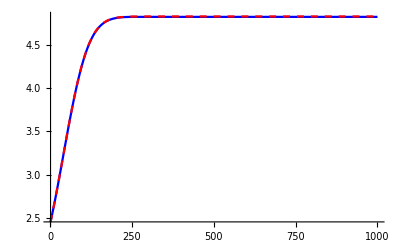

```mathematica
DiscretePlot[
{y[n],ExactSolution[t[n],r0]},
{n,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```

Numerical and exact solution coincide over the entire range. Note, however, that if we choose a time step h 10 times smaller, and integrate,

```mathematica
h=0.001;
integrate[0,10,tol]
```

Integration performed from t=0 to t=10 in m=10000 steps.

we obtain the following numerical solution (blue),

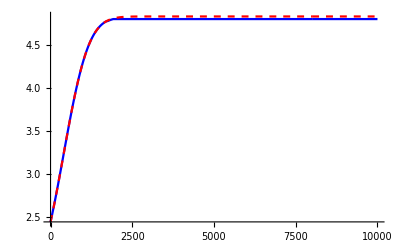

```mathematica
DiscretePlot[
{y[n],ExactSolution[t[n],r0]},
{n,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```

which is not as good as the previous one! Perhaps this happens because we don’t update the value of the Jacobian over a much larger number of steps.

A nonlinear system of two equation

### The differential system and its exact solution

Here we define the differential equation to integrate and find its exact solution.

```mathematica
ClearAll[x,y,z,X,F,f,g];
```

```mathematica
Clear[f,g];
f[y_,z_]:=-z y;
g[y_]:=y;
```

```mathematica
DSolve[{
D[y[t,r0],t]==-z[t,r0]y[t,r0],
D[z[t,r0],t]==y[t,r0],                      (* equations *)

y[0,r0]==0.4524,
z[0,r0]==0.7644                                           (* Initial data *)

},{y[t,r0],z[t,r0]},{t}]//Simplify//Quiet//Echo/@#&;
```

{z[t,r0]→1.22029 √(Tanh[0.735483-0.610145 t]^2),y[t,r0]→0.744554-0.744554 Tanh[0.735483-0.610145 t]^2}

{z[t,r0]→1.22029 √(Tanh[0.735483+0.610145 t]^2),y[t,r0]→0.744554-0.744554 Tanh[0.735483+0.610145 t]^2}

```mathematica
Clear[x];
x[n_]={y[n],z[n]};
```

```mathematica
Clear[F];
F[t_,r_,{y_,z_}]:={f[y,z],g[y]};
```

```mathematica
Clear[ExactSolution];
ExactSolution[t_]:={0.74455368-0.74455368 Tanh[0.7354833408382715+0.6101449336018452 t]^2,1.2202898672036904 √(Tanh[0.7354833408382715+0.6101449336018452 t]^2)}
```

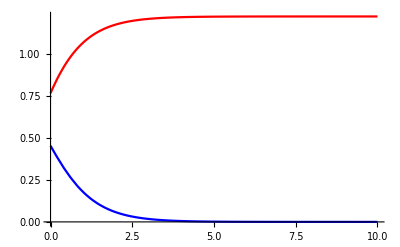

```mathematica
Plot[{0.74455368-0.74455368 Tanh[0.7354833408382715+0.6101449336018452 t]^2,1.2202898672036904 √(Tanh[0.7354833408382715+0.6101449336018452 t]^2)},{t,0,10},PlotStyle->{Blue,Red}]
```

### The numerical integration of the system

```mathematica
v=2;                                                             (* number of unkown variables *)
r0=1;                                                          (* fixed radius or collocation point *)
t0=0;                                                          (* initial time *)
h=0.01;                                                     (* time step *)
t[0]=t0;
y[0]=0.4524;
z[0]=0.7644;                                       (* initial data *)
𝕀[1]=1;                                                   (* utility function *)
𝕀[m_]:=IdentityMatrix[m];
```

Y[n,i][k] means value of the variable Y at time step n, stage i and iteration k.

```mathematica
Clear[step$n$stage$i];
step$n$stage$i[n_,i_]:=x[n]+h Sum[A⟦i,j⟧F[t[n]+c⟦j,1⟧h,r0, Y[n,j]],{j,1,s}]//Simplify
```

Compare the above formula with (81) in the last excerpt.

Now we compute the Jacobian, and keep it the same for all time steps (it should be updated after some time).

```mathematica
Clear[J];
J[n_]:={
{D[F[t[np],r0,step$n$stage$i[np,1]]⟦1⟧,y[np]]/.{np->n}, 
D[F[t[np],r0,step$n$stage$i[np,1]]⟦1⟧,z[np]]/.{np->n}},
{D[F[t[np],r0,step$n$stage$i[np,1]]⟦2⟧,y[np]]/.{np->n},
D[F[t[np],r0,step$n$stage$i[np,1]]⟦2⟧,z[np]]/.{np->n}}
}
```

```mathematica
J[n]//MatrixForm
```

(0.-z[n] | 0.-y[n]
1 | 0)

```mathematica
J[0]//MatrixForm
```

(-0.7644 | -0.4524
1 | 0)

We define the matrix ℕ in (83).

```mathematica
ℕ[n_,i_]:=𝕀[v]-h A⟦i,i⟧J[n]
```

Now we are set the initial data. X at time 0, stage 1, iteration 0 is equal to the initial data,

```mathematica
X[0,1][0]={0.4524,0.7644};
```

At this point, we write the functions to perform the modified Newton iteration at each stage (the following functions are at a fixed r or collocation point).

In C++, the LU decomposition has to be implemented in the following loop. Here in Mathematica, we just use Solve. The following loop performs the Newton iteration for a given stage,

```mathematica
tol=10^-4;
```

```mathematica
Clear[computeStage];
computeStage[n_,i_,tolerance_]:=Module[{dis$y,dis$z,k},
dis$y=10^3;
dis$y=10^3;
k=0;
While[(Abs[dis$y]>tolerance || Abs[dis$z]>tolerance)&&k<100,
{dis$y,dis$z}=Solve[
ℕ[n,i].{xx,yy}==-(X[n,i][k]-x[n])+h Sum[A⟦i,j⟧F[t[n]+c⟦j,1⟧h,r0, X[n,j][n$iteration[j]]],{j,1,i-1}]
    +h  Sum[A⟦i,s⟧F[t[n]+c⟦s,1⟧h,r0, X[n,s][k]],{j,i,s}],{xx,yy}
]⟦1,All,2⟧;
X[n,i][k+1]=X[n,i][k]+{dis$y,dis$z};
++k;
];
n$iteration[i]=k-1;
X[n,i+1][0]=X[n,i][k-1];
]
```

The following function performs the loop over the stages within a time step,

```mathematica
Clear[computeStep];
computeStep[n_,tol_]:=Module[{σ},
For[σ=1,σ≤s,σ++,
computeStage[n,σ,tol];
];
x[n+1]=X[n,σ][0];
y[n+1]=X[n,σ][0]⟦1⟧;
z[n+1]=X[n,σ][0]⟦2⟧;
X[n+1,1][0]=X[n,σ][0];
]
```

The following loop finally integrates up until t_1,

```mathematica
Clear[integrate];
integrate[t0_,t1_,tol_]:=Module[{m},
m=0;
t[0]=t0;
Monitor[
While[t[m]≤t1,
computeStep[m,tol];
t[m+1]=t[m]+h;
++m;
],
t[m]];
m$size=m-1;
Print["Integration performed from t="<>ToString[t0]<>" to t="<>ToString[t1]<>" in m="<>ToString[m$size]<>" steps."];
]
```

Now comes the actual integration,

```mathematica
h=0.01;
integrate[0,10,tol]
```

Integration performed from t=0 to t=10 in m=1000 steps.

We compare the numerical solution (blue) with the exact solution (red dashed),

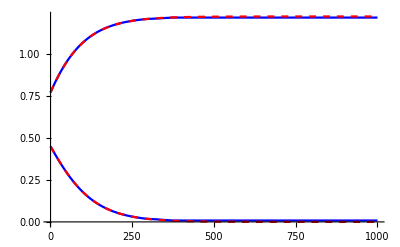

```mathematica
DiscretePlot[
{x[m],ExactSolution[t[m]]},
{m,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```

Numerical and exact solution coincide over the entire range.

I played a little bit with the time step. It seems that the smaller the time step, the smaller should be the tolerance in order to get an accurate solution. For example,

Here the time step is h=10^-3  and the tolerance is tol=10^-4 (same tolerance as before, but h → h/10),

Integration performed from t=0 to t=10 in m=10000 steps.

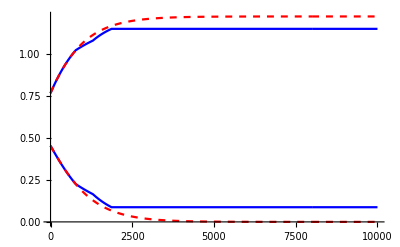

```mathematica
h=0.001;
integrate[0,10,tol]
DiscretePlot[
{x[m],ExactSolution[t[m]]},
{m,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```

The above result is not nice. Now we try the same time step as abopve, but a tolerance of 10^-5= tol/10.

Integration performed from t=0 to t=10 in m=10000 steps.

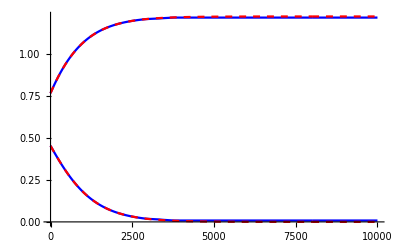

```mathematica
h=0.001;
integrate[0,10,10^-5]
DiscretePlot[
{x[m],ExactSolution[t[m]]},
{m,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```

This is better, and comparable with h=10^-2, tol=10^-4! Hence, the dependence seems to be linear. Let’s try with even smaller tolerance,

Integration performed from t=0 to t=10 in m=10000 steps.

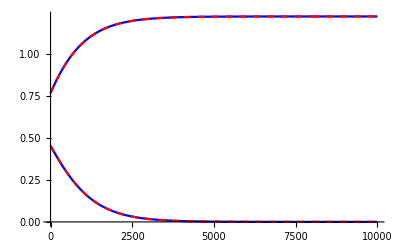

```mathematica
h=0.001;
integrate[0,10,10^-8]
DiscretePlot[
{x[m],ExactSolution[t[m]]},
{m,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```

Towards C++

### LU decomposition – algorithm to be exported to C++

#### The LU decomposition

The algorithm is taken from this webpage.

```mathematica
𝕕=10;
```

```mathematica
𝕃=Table[0,{i,1,𝕕},{j,1,𝕕}];
𝕌=Table[0,{i,1,𝕕},{j,1,𝕕}];
𝕄=RandomReal[{-5,5},{𝕕,𝕕}];
Module[{i,j,k,m,sum},
For[i=1,i≤𝕕,i++,

(* Upper triangular *)
For[k=i,k≤𝕕,k++,
sum=0;
For[j=1,j<i,j++,
sum+=𝕃⟦i,j⟧*𝕌⟦j,k⟧;
];
𝕌⟦i,k⟧=𝕄⟦i,k⟧-sum;
];

(* Lower triangular *)
For[k=i,k≤𝕕,k++,
If[i==k,
𝕃⟦i,i⟧=1;,
sum=0;
For[j=1,j<i,j++,
sum+=𝕃⟦k,j⟧*𝕌⟦j,i⟧;
];
𝕃⟦k,i⟧=(𝕄⟦k,i⟧-sum)/𝕌⟦i,i⟧;
];
];

];
];
𝕄//MatrixForm
Det[𝕄]
𝕃//MatrixForm
𝕌//MatrixForm
𝕃.𝕌//MatrixForm
𝕃.𝕌==𝕄//Chop
```

(1.628 | -3.57847 | 1.29413
-2.53307 | -2.89434 | -2.6006
4.32746 | -0.818777 | 3.90159)

1.94836

(1 | 0 | 0
-1.55594 | 1 | 0
2.65814 | -1.02731 | 1)

(1.628 | -3.57847 | 1.29413
0 | -8.46222 | -0.587
0 | 0 | -0.141426)

(1.628 | -3.57847 | 1.29413
-2.53307 | -2.89434 | -2.6006
4.32746 | -0.818777 | 3.90159)

True

```mathematica
Clear[LUDecompose];
LUDecompose[𝕄_]:=Module[{𝕃,𝕌,𝕕,i,j,k,m,sum},
𝕕=Length@𝕄;
𝕃=Table[0,{i,1,𝕕},{j,1,𝕕}];
𝕌=Table[0,{i,1,𝕕},{j,1,𝕕}];
For[i=1,i≤𝕕,i++,

(* Upper triangular *)
For[k=i,k≤𝕕,k++,
sum=0;
For[j=1,j<i,j++,
sum+=𝕃⟦i,j⟧*𝕌⟦j,k⟧;
];
𝕌⟦i,k⟧=𝕄⟦i,k⟧-sum;
];

(* Lower triangular *)
For[k=i,k≤𝕕,k++,
If[i==k,
𝕃⟦i,i⟧=1;,
sum=0;
For[j=1,j<i,j++,
sum+=𝕃⟦k,j⟧*𝕌⟦j,i⟧;
];
𝕃⟦k,i⟧=(𝕄⟦k,i⟧-sum)/𝕌⟦i,i⟧;
];
];
];
Return[{𝕃,𝕌}];
];
```

```mathematica
𝕄=RandomInteger[{-5,5},{𝕕,𝕕}];
𝕄//MatrixForm
Det[𝕄]
{Low,Upp}=LUDecompose[𝕄];
Low//MatrixForm
Upp//MatrixForm
Low.Upp//MatrixForm
Low.Upp==𝕄 //Chop
```

(-4 | -1 | 4 | 4 | -4 | 4 | 5 | 2 | 1 | 3
-2 | -2 | 1 | -2 | 4 | -5 | 4 | 3 | 1 | 0
5 | -5 | -4 | 5 | -5 | 0 | 4 | 5 | 3 | 5
-1 | 3 | -5 | -5 | 2 | 0 | 1 | 4 | 0 | 0
2 | -4 | -2 | 2 | -2 | 0 | -2 | 3 | -1 | -1
-1 | -5 | 1 | 2 | -3 | -1 | -3 | -5 | -2 | 3
-5 | -1 | 1 | 4 | 3 | -1 | -5 | 2 | -2 | -3
0 | -5 | 0 | -1 | -2 | 1 | -1 | -1 | 2 | -5
-3 | 4 | -3 | -1 | 1 | -2 | -1 | 0 | 1 | -5
-4 | -5 | 3 | 1 | 0 | 3 | -3 | -1 | -5 | 5)

-33486921

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5/4 | 25/6 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | -13/6 | -49/31 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 | 3 | 18/31 | 4/213 | 1 | 0 | 0 | 0 | 0 | 0
1/4 | 19/6 | 19/31 | -83/852 | 2879/800 | 1 | 0 | 0 | 0 | 0
5/4 | -1/6 | -25/31 | 205/284 | -7803/800 | -6791/2363 | 1 | 0 | 0 | 0
0 | 10/3 | 20/31 | -151/852 | 5443/800 | 3071/2363 | -48661/96834 | 1 | 0 | 0
3/4 | -19/6 | -55/31 | 475/426 | -2023/400 | -86/139 | 33337/48417 | -884959/613445 | 1 | 0
1 | 8/3 | 10/31 | -29/852 | 349/160 | -1035/2363 | -5375/32278 | 1185678/613445 | -5851/4113 | 1)

(-4 | -1 | 4 | 4 | -4 | 4 | 5 | 2 | 1 | 3
0 | -3/2 | -1 | -4 | 6 | -7 | 3/2 | 2 | 1/2 | -3/2
0 | 0 | 31/6 | 80/3 | -35 | 205/6 | 4 | -5/6 | 13/6 | 15
0 | 0 | 0 | 852/31 | -1219/31 | 1173/31 | 289/31 | 202/31 | 132/31 | 611/31
0 | 0 | 0 | 0 | -200/213 | 174/71 | -1384/213 | -349/213 | -237/71 | -869/213
0 | 0 | 0 | 0 | 0 | -2363/400 | 321/25 | -3833/800 | 5813/800 | 11527/800
0 | 0 | 0 | 0 | 0 | 0 | -96834/2363 | -83398/2363 | -38207/2363 | -17757/2363
0 | 0 | 0 | 0 | 0 | 0 | 0 | -613445/96834 | 233986/48417 | -14983/16139
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8156079/1226890 | -18707511/1226890
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5629/1371)

(-4 | -1 | 4 | 4 | -4 | 4 | 5 | 2 | 1 | 3
-2 | -2 | 1 | -2 | 4 | -5 | 4 | 3 | 1 | 0
5 | -5 | -4 | 5 | -5 | 0 | 4 | 5 | 3 | 5
-1 | 3 | -5 | -5 | 2 | 0 | 1 | 4 | 0 | 0
2 | -4 | -2 | 2 | -2 | 0 | -2 | 3 | -1 | -1
-1 | -5 | 1 | 2 | -3 | -1 | -3 | -5 | -2 | 3
-5 | -1 | 1 | 4 | 3 | -1 | -5 | 2 | -2 | -3
0 | -5 | 0 | -1 | -2 | 1 | -1 | -1 | 2 | -5
-3 | 4 | -3 | -1 | 1 | -2 | -1 | 0 | 1 | -5
-4 | -5 | 3 | 1 | 0 | 3 | -3 | -1 | -5 | 5)

True

```mathematica
𝔸={{-4,0,-1,2,-1,5,3,-4,-2,2},{-3,5,-5,-3,3,1,2,1,-2,4},{2,1,-1,3,4,1,-1,1,1,-2},{3,4,-3,5,4,4,3,4,-2,0},{-4,-4,5,-5,-5,4,-2,-5,-1,0},{-2,-5,-2,-1,3,-2,1,5,-1,0},{0,5,0,-1,5,3,5,-1,3,-1},{1,-2,4,0,-5,5,3,-4,-4,-3},{0,3,-3,-5,3,1,-1,-5,3,1},{0,-1,-1,-3,3,2,-2,-2,-1,2}};
𝔸//MatrixForm
Det[𝔸]
{Low,Upp}=LUDecompose[𝔸];
Low//N//MatrixForm
Upp//N//MatrixForm
Low.Upp//MatrixForm
Low.Upp==𝔸//Chop
```

(-4 | 0 | -1 | 2 | -1 | 5 | 3 | -4 | -2 | 2
-3 | 5 | -5 | -3 | 3 | 1 | 2 | 1 | -2 | 4
2 | 1 | -1 | 3 | 4 | 1 | -1 | 1 | 1 | -2
3 | 4 | -3 | 5 | 4 | 4 | 3 | 4 | -2 | 0
-4 | -4 | 5 | -5 | -5 | 4 | -2 | -5 | -1 | 0
-2 | -5 | -2 | -1 | 3 | -2 | 1 | 5 | -1 | 0
0 | 5 | 0 | -1 | 5 | 3 | 5 | -1 | 3 | -1
1 | -2 | 4 | 0 | -5 | 5 | 3 | -4 | -4 | -3
0 | 3 | -3 | -5 | 3 | 1 | -1 | -5 | 3 | 1
0 | -1 | -1 | -3 | 3 | 2 | -2 | -2 | -1 | 2)

-38621414

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.75 | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.5 | 0.2 | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.75 | 0.8 | 0.538462 | 1. | 0. | 0. | 0. | 0. | 0. | 0.
1. | -0.8 | -4. | 1.20619 | 1. | 0. | 0. | 0. | 0. | 0.
0.5 | -1. | 8.84615 | -6.68041 | -2.20287 | 1. | 0. | 0. | 0. | 0.
0. | 1. | -6.53846 | 4.76289 | 2.18492 | -0.755231 | 1. | 0. | 0. | 0.
-0.25 | -0.4 | -3.15385 | 1.89691 | 0.631957 | 0.0530529 | 0.0903035 | 1. | 0. | 0.
0. | 0.6 | 0.692308 | -0.762887 | -0.182226 | 0.382579 | -0.205701 | 1.9588 | 1. | 0.
0. | -0.2 | 2.84615 | -2.39175 | -0.611311 | 0.637596 | -0.216282 | 1.27095 | 0.325346 | 1.)

(-4. | 0. | -1. | 2. | -1. | 5. | 3. | -4. | -2. | 2.
0. | 5. | -4.25 | -4.5 | 3.75 | -2.75 | -0.25 | 4. | -0.5 | 2.5
0. | 0. | -0.65 | 4.9 | 2.75 | 4.05 | 0.55 | -1.8 | 0.1 | -1.5
0. | 0. | 0. | 7.46154 | -1.23077 | 7.76923 | 5.15385 | -1.23077 | -3.15385 | 0.307692
0. | 0. | 0. | 0. | 11.4845 | 3.62887 | -9.21649 | -3.51546 | 4.80412 | -6.37113
0. | 0. | 0. | 0. | 0. | 16.8187 | 8.51167 | 10.9569 | -11.8707 | 2.78995
0. | 0. | 0. | 0. | 0. | 0. | 10.8645 | 5.04878 | -0.286507 | 1.25427
0. | 0. | 0. | 0. | 0. | 0. | 0. | -5.55787 | -0.782411 | -3.04943
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.71532 | 4.77606
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.42464)

(-4 | 0 | -1 | 2 | -1 | 5 | 3 | -4 | -2 | 2
-3 | 5 | -5 | -3 | 3 | 1 | 2 | 1 | -2 | 4
2 | 1 | -1 | 3 | 4 | 1 | -1 | 1 | 1 | -2
3 | 4 | -3 | 5 | 4 | 4 | 3 | 4 | -2 | 0
-4 | -4 | 5 | -5 | -5 | 4 | -2 | -5 | -1 | 0
-2 | -5 | -2 | -1 | 3 | -2 | 1 | 5 | -1 | 0
0 | 5 | 0 | -1 | 5 | 3 | 5 | -1 | 3 | -1
1 | -2 | 4 | 0 | -5 | 5 | 3 | -4 | -4 | -3
0 | 3 | -3 | -5 | 3 | 1 | -1 | -5 | 3 | 1
0 | -1 | -1 | -3 | 3 | 2 | -2 | -2 | -1 | 2)

True

#### Solving a linear system through the LU decomposition

Once you have the LU decomposition of a matrix M, you can easily solve the system Mx=b for x, since you can write LUx=b, set Ux=y and solve Ly=b first, and then Ux=y.

Solving a system in this way reduces the number of the needed operations from O(n^3) to O(n^2).

```mathematica
b=RandomReal[{0,1},{𝕕}];
y=Table[0,{𝕕}];
Module[{i,j},
For[i=1,i≤𝕕,i++,
y⟦i⟧=b⟦i⟧;
];
For[i=2,i≤𝕕,i++,
For[j=i,j≤𝕕,j++,
y⟦j⟧=y⟦j⟧-𝕃⟦j,i-1⟧y⟦i-1⟧
]
]
];
𝕃.y==b
```

True

```mathematica
x=Table[0,{𝕕}];
Module[{i,j},
For[i=𝕕,i≥ 1,i--,
x⟦i⟧=y⟦i⟧;
];
For[i=𝕕,i≥ 1,i--,
For[j=i+1,j≤𝕕,j++,
x⟦i⟧=x⟦i⟧-𝕌⟦i,j⟧x⟦j⟧
];
x⟦i⟧=x⟦i⟧/𝕌⟦i,i⟧;
]
];
𝕌.x==y
```

True

```mathematica
𝕄.x==b
```

False

#### Combining the algorithms to solve a generic linear system

```mathematica
Clear[SolveLinearSystem];
SolveLinearSystem[MatrixOfCoefficients_?MatrixQ,RHSVector_?VectorQ]:=
Module[{i,j,𝕪,𝕩,𝕕,𝕃,𝕌},
𝕕=Length@MatrixOfCoefficients;
𝕪=Table[0,{𝕕}];
𝕩=Table[0,{𝕕}];
{𝕃,𝕌}=LUDecompose[MatrixOfCoefficients];
For[i=1,i≤𝕕,i++,
𝕪⟦i⟧=RHSVector⟦i⟧;
];
For[i=2,i≤𝕕,i++,
For[j=i,j≤𝕕,j++,
𝕪⟦j⟧=𝕪⟦j⟧-𝕃⟦j,i-1⟧𝕪⟦i-1⟧
]
];
For[i=𝕕,i≥ 1,i--,
𝕩⟦i⟧=𝕪⟦i⟧;
];
For[i=𝕕,i≥ 1,i--,
For[j=i+1,j≤𝕕,j++,
𝕩⟦i⟧=𝕩⟦i⟧-𝕌⟦i,j⟧𝕩⟦j⟧
];
𝕩⟦i⟧=𝕩⟦i⟧/𝕌⟦i,i⟧;
];
Return[𝕩];
]
```

```mathematica
𝕄=RandomReal[{-5,5},{𝕕,𝕕}];
𝕓=RandomReal[{-10,10},{𝕕}];
𝕩=SolveLinearSystem[𝕄,𝕓]
𝕄.𝕩==𝕓
```

{0.742556,-1.46019,-2.69178}

True

```mathematica
Clear[SolveLinearSystem$LU];
SolveLinearSystem$LU[𝕃_?MatrixQ,𝕌_?MatrixQ,RHSVector_?VectorQ]:=
Module[{i,j,𝕪,𝕩,𝕕},
𝕕=Length@RHSVector;
𝕪=Table[0,{𝕕}];
𝕩=Table[0,{𝕕}];
For[i=1,i≤𝕕,i++,
𝕪⟦i⟧=RHSVector⟦i⟧;
];
For[i=2,i≤𝕕,i++,
For[j=i,j≤𝕕,j++,
𝕪⟦j⟧=𝕪⟦j⟧-𝕃⟦j,i-1⟧𝕪⟦i-1⟧
]
];
For[i=𝕕,i≥ 1,i--,
𝕩⟦i⟧=𝕪⟦i⟧;
];
For[i=𝕕,i≥ 1,i--,
For[j=i+1,j≤𝕕,j++,
𝕩⟦i⟧=𝕩⟦i⟧-𝕌⟦i,j⟧𝕩⟦j⟧
];
𝕩⟦i⟧=𝕩⟦i⟧/𝕌⟦i,i⟧;
];
Return[𝕩];
]
```

```mathematica
𝕄=RandomReal[{-5,5},{𝕕,𝕕}];
{𝕃,𝕌}=LUDecompose[𝕄];
𝕓=RandomReal[{-10,10},{𝕕}];
𝕩=SolveLinearSystem$LU[𝕃,𝕌,𝕓]
{𝕄.𝕩,𝕓}
```

{0.767939,-3.09752,-1.1762,0.0427864,0.806738,1.05323,-0.555692,-1.98133,-1.35481,0.240272}

{{1.11309,1.36356,-0.184269,1.18384,5.15471,-5.5735,3.62594,-3.70491,8.8407,6.08612},{1.11309,1.36356,-0.184269,1.18384,5.15471,-5.5735,3.62594,-3.70491,8.8407,6.08612}}

```mathematica
{𝕃,𝕌}=LUDecompose[𝔸];
𝕓={-1,-1,10,10,6,7,-2,-3,6,5};
𝕩=SolveLinearSystem$LU[𝕃,𝕌,𝕓]//N
𝔸.𝕩==𝕓
```

{-0.251102,-0.84925,-2.74851,-0.719948,-0.887013,3.83469,-2.27776,2.12307,1.9726,-2.05136}

True

### The DIRK algorithm

#### The differential system and its exact solution

Here we define the differential equation to integrate and find its exact solution.

```mathematica
ClearAll[x,y,z,X,F,f,g];
```

```mathematica
Clear[f,g];
f[y_,z_]:=-z y;
g[y_]:=y;
```

```mathematica
DSolve[{
D[y[t,r0],t]==-z[t,r0]y[t,r0],
D[z[t,r0],t]==y[t,r0],                      (* equations *)

y[0,r0]==0.4524,
z[0,r0]==0.7644                                           (* Initial data *)

},{y[t,r0],z[t,r0]},{t}]//Simplify//Quiet//Echo/@#&;
```

{z[t,r0]→1.22029 √(Tanh[0.735483-0.610145 t]^2),y[t,r0]→0.744554-0.744554 Tanh[0.735483-0.610145 t]^2}

{z[t,r0]→1.22029 √(Tanh[0.735483+0.610145 t]^2),y[t,r0]→0.744554-0.744554 Tanh[0.735483+0.610145 t]^2}

```mathematica
Clear[x];
x[n_]={y[n],z[n]};
```

```mathematica
Clear[F];
F[t_,r_,{y_,z_}]:={f[y,z],g[y]};
```

```mathematica
Clear[ExactSolution];
ExactSolution[t_]:={0.74455368-0.74455368 Tanh[0.7354833408382715+0.6101449336018452 t]^2,1.2202898672036904 √(Tanh[0.7354833408382715+0.6101449336018452 t]^2)}
```

```mathematica
Plot[{0.74455368-0.74455368 Tanh[0.7354833408382715+0.6101449336018452 t]^2,1.2202898672036904 √(Tanh[0.7354833408382715+0.6101449336018452 t]^2)},{t,0,10},PlotStyle->{Blue,Red}]
```

-Graphics-

#### The numerical integration of the system

```mathematica
s=4;
v=2;                                                             (* number of unkown variables *)
r0=1;                                                          (* fixed radius or collocation point *)
t0=0;                                                          (* initial time *)
h=0.01;                                                     (* time step *)
t[0]=t0;
y[0]=0.4524;
z[0]=0.7644;                                       (* initial data *)
𝕀[1]=1;                                                   (* utility function *)
𝕀[m_]:=IdentityMatrix[m];
```

Y[n,i][k] means value of the variable Y at time step n, stage i and iteration k.

```mathematica
Clear[step$n$stage$i];
step$n$stage$i[n_,i_]:=x[n]+h Sum[A⟦i,j⟧F[t[n]+c⟦j,1⟧h,r0, Y[n,j]],{j,1,s}]//Simplify
```

Compare the above formula with (81) in the last excerpt.

Now we compute the Jacobian, and keep it the same for all time steps (it should be updated after some time).

```mathematica
Clear[J];
J[n_]:={
{D[F[t[np],r0,step$n$stage$i[np,1]]⟦1⟧,y[np]]/.{np->n}, 
D[F[t[np],r0,step$n$stage$i[np,1]]⟦1⟧,z[np]]/.{np->n}},
{D[F[t[np],r0,step$n$stage$i[np,1]]⟦2⟧,y[np]]/.{np->n},
D[F[t[np],r0,step$n$stage$i[np,1]]⟦2⟧,z[np]]/.{np->n}}
}
```

```mathematica
J[0]//MatrixForm
```

(-0.7644 | -0.4524
1 | 0)

We define the matrix ℕ in (83),

```mathematica
ℕ[n_,i_]:=𝕀[v]-h A⟦i,i⟧J[n]
```

```mathematica
𝕣[n_,i_,k_]:=-(X[n,i][k]-x[n])+h Sum[A⟦i,j⟧F[t[n]+c⟦j,1⟧h,r0, X[n,j][n$iteration[j]]],{j,1,i-1}]+h  Sum[A⟦i,s⟧F[t[n]+c⟦s,1⟧h,r0, X[n,s][k]],{j,i,s}];
```

Now we are set the initial data. X at time 0, stage 1, iteration 0 is equal to the initial data,

```mathematica
X[0,1][0]={0.4524,0.7644};
```

At this point, we write the functions to perform the modified Newton iteration at each stage (the following functions are at a fixed r or collocation point).

The following loop performs the Newton iteration for a given stage,

```mathematica
tol=10^-4;
```

```mathematica
Clear[computeStage];
computeStage[n_,i_,tolerance_]:=Module[{dis$y,dis$z,k},
dis$y=10^3;
dis$y=10^3;
k=0;
While[(Abs[dis$y]>tolerance || Abs[dis$z]>tolerance)&&k<100,
{dis$y,dis$z}=SolveLinearSystem$LU[
𝕃,𝕌,𝕣[n,i,k]
];
X[n,i][k+1]=X[n,i][k]+{dis$y,dis$z};
++k;
];
n$iteration[i]=k-1;
X[n,i+1][0]=X[n,i][k-1];
]
```

The following function performs the loop over the stages within a time step, updating the Jacobian at each step (the level of update of the Jacobian should be chosen by the user in C++),

```mathematica
Clear[computeStep];
computeStep[n_,tol_]:=Module[{σ},
{𝕃,𝕌}=LUDecompose[ℕ[n,1]];
For[σ=1,σ≤s,σ++,
computeStage[n,σ,tol];
];
x[n+1]=X[n,σ][0];
y[n+1]=X[n,σ][0]⟦1⟧;
z[n+1]=X[n,σ][0]⟦2⟧;
X[n+1,1][0]=X[n,σ][0];
]
```

The following loop finally integrates up until t_1,

```mathematica
Clear[integrate];
integrate[t0_,t1_,tol_]:=Module[{m},
m=0;
t[0]=t0;
Monitor[
While[t[m]≤t1,
computeStep[m,tol];
t[m+1]=t[m]+h;
++m;
],
t[m]];
m$size=m-1;
Print["Integration performed from t="<>ToString[t0]<>" to t="<>ToString[t1]<>" in m="<>ToString[m$size]<>" steps."];
]//timed
```

Now comes the actual integration,

```mathematica
h=0.01;
integrate[0,10,tol]
```

Integration performed from t=0 to t=10 in m=1000 steps.

Elapsed time = 1.7100000

We compare the numerical solution (blue) with the exact solution (red dashed),

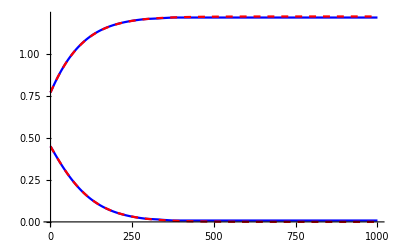

```mathematica
DiscretePlot[
{x[m],ExactSolution[t[m]]},
{m,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```

Numerical and exact solution coincide over the entire range.

I played a little bit with the time step. It seems that the smaller the time step, the smaller should be the tolerance in order to get an accurate solution. For example,

Here the time step is h=10^-3  and the tolerance is tol=10^-4 (same tolerance as before, but h → h/10),

```mathematica
h=0.001;
integrate[0,10,tol]
DiscretePlot[
{x[m],ExactSolution[t[m]]},
{m,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```

Integration performed from t=0 to t=10 in m=10000 steps.

-Graphics-

The above result is not nice. Now we try the same time step as abopve, but a tolerance of 10^-5= tol/10.

```mathematica
h=0.001;
integrate[0,10,10^-5]
DiscretePlot[
{x[m],ExactSolution[t[m]]},
{m,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```

Integration performed from t=0 to t=10 in m=10000 steps.

-Graphics-

This is better, and comparable with h=10^-2, tol=10^-4! Hence, the dependence seems to be linear. Let’s try with even smaller tolerance,

Integration performed from t=0 to t=10 in m=10000 steps.

Elapsed time = 19.9730000

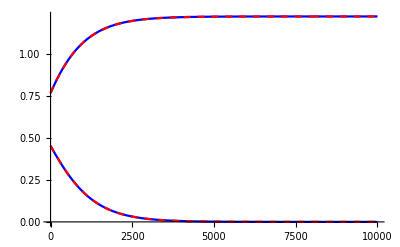

```mathematica
h=0.001;
integrate[0,10,10^-8]
DiscretePlot[
{x[m],ExactSolution[t[m]]},
{m,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```

Exportation to C++

#### Defining the functions to translate into C++

```mathematica
toStringCForm[e_]:=ToString@CForm@e
```

```mathematica
StringReplacements={"κ"->"k_",
"β(0)"->"b_0","β(1)"->"b_1","β(2)"->"b_2","β(3)"->"b_3","β(4)"->"b_4",
"ρ"->"rho","τ"->"tau","gσ"->"gsig","fσ"->"fsig","gAσ"->"gAsig","fAσ"->"fAsig","*"->" * ","/"->" / ","•"->"","Lap"->"Alp","p1"->"p","q1"->"q","TrgK"->"gtrK","TrfK"->"ftrK","TrgA1"->"gtrA","TrgA2"->"gtrAv","TrfA1"->"ftrA","TrfA2"->"ftrAv","TrgA"->"gtrA","TrfA"->"ftrA","detγc"->"gdet","detφc"->"fdet","Λ1"->"L","Λ"->"L","λ"->"Lt","J$A1f"->"fJA1","J$A2f"->"fJA2","J$A1g"->"gJA1","J$A2g"->"gJA2","J$Kf"->"fJK","J$Kg"->"gJK","J$Λg"->"gJL","J$Λf"->"fJL","gj1"->"gj","fj1"->"fj","ratio"->"R","gD$Vd"->"pfD","gS$Vd"->"pfS","gτ$Vd"->"pftau","gv$V"->"pfv","gjb1"->"gjb_u","fjb1"->"fjb_u","gDb"->"gDB","fDb"->"fDB","gDσ"->"gDsig","fDσ"->"fDsig","η"->"eta","B1"->"Bq","gShi1"->"gBet","gShir"->"gBetr","fShi1"->"fBet","fShir"->"fBetr","$"->""};
```

```mathematica
Clear[exportCppFunction]
exportCppFunction[{name_,symbol_,e_}]:=Block[
{str,out,j=0},
str=Characters@StringReplace[
InsertLinebreaks[StringReplace[toStringCForm[e],
StringReplacements
],75],
{"+\n"->"\n+ ","-\n"->"\n- ","*\n"->"\n* ","/\n"->"\n/ "}
];
out=Table[
If[str⟦i⟧==="(",++j,If[str⟦i⟧===")",--j]];
If[str⟦i⟧==="\n","\n    /*"<>ToString@j<>"*/  ",str⟦i⟧],{i,Length@str}];
"Real BimetricEvolve::"<>name<>"( Int m, Int n )\n{\n    return "<>StringJoin[out]<>";\n}\n"
]
```

```mathematica
Clear[powerCppRules];
powerCppRules[e_]:=e//.{
Power[ⅇ,x_]:>exp[x],
f_[args1___,Power[ⅇ,x_],args2___]:>f[args1,exp[x],args2],
g_[args___,f_[args1___,Power[ⅇ,x_],args2___],args3___]:>g[args,f[args1,exp[x],args2],args3],
h_[args0___,g_[args___,f_[args1___,Power[ⅇ,x_],args2___],args3___],args4___]:>h[args0,g[args,f[args1,exp[x],args2],args3],args4],
l_[args6___,h_[args0___,g_[args___,f_[args1___,Power[ⅇ,x_],args2___],args3___],args4___],args5___]:>l[args6,h[args0,g[args,f[args1,exp[x],args2],args3],args4],args5],
m_[args7___,l_[args6_,h_[args0___,g_[args___,f_[args1___,Power[ⅇ,x_],args2___],args3___],args4___],args5___],args8___]:>m[args7,l[args6,h[args0,g[args,f[args1,exp[x],args2],args3],args4],args5],args8],
Sqrt[v_]:>sqrt[v],
Power[v_,-1]:>1/v,
Power[v_,1/2]:>1/sqrt[v],Power[v_,-1/2]:>1/sqrt[v],
Power[v_,2]:>pow2[v],Power[v_,-2]:>1/pow2[v],
Power[v_,3]:>pow3[v],Power[v_,-3]:>1/pow3[v],
Power[v_,3/2]:>pow15[v],Power[v_,-3/2]:>1/pow15[v]
}
```

```mathematica
riffleCppLines[e_]:=StringReplace[StringJoin[Riffle[e,"\n"]],{"$"->"_"}]
```

```mathematica
Flatten@{(D[UnderBar[#],r] UnderBar[gDconf]->gconfD[UnderBar[#]])&/@{gShi1},(UnderBar[fDconf] D[UnderBar[#],r]->fconfD[UnderBar[#]])&/@{fShi1},(D[UnderBar[#],r] UnderBar[gΛ1]->gΛD[UnderBar[#]])&/@{gShi1},(UnderBar[fΛ1] D[UnderBar[#],r]->fΛD[UnderBar[#]])&/@{fShi1},(D[UnderBar[#],r] UnderBar[gDA]->gDAD[UnderBar[#]])&/@{gShi1},(UnderBar[fDA] D[UnderBar[#],r]->fDAD[UnderBar[#]])&/@{fShi1},(D[UnderBar[#],r] UnderBar[gDb]->gDbD[UnderBar[#]])&/@{gShi1},(UnderBar[fDb] D[UnderBar[#],r]->fDbD[UnderBar[#]])&/@{fShi1},(UnderBar[gShi1] UnderBar[gDA]^2->gShiD[UnderBar[g$A]] UnderBar[gDA]/UnderBar[g$A]),(UnderBar[fShi1] UnderBar[fDA]^2->fShiD[UnderBar[f$A]] UnderBar[fDA]/UnderBar[f$A]),(UnderBar[gShi1] UnderBar[gDb]^2->gShiD[UnderBar[g$b]] UnderBar[gDb]/UnderBar[g$b]),(UnderBar[fShi1] UnderBar[fDb]^2->fShiD[UnderBar[f$b]] UnderBar[fDb]/UnderBar[f$b])}//printNice
```

printNice[{0→gconfD[UnderBar[gShi1]],0→fconfD[UnderBar[fShi1]],0→gΛD[UnderBar[gShi1]],0→fΛD[UnderBar[fShi1]],0→gDAD[UnderBar[gShi1]],0→fDAD[UnderBar[fShi1]],0→gDbD[UnderBar[gShi1]],0→fDbD[UnderBar[fShi1]],UnderBar[gDA]^2 UnderBar[gShi1]→(gShiD[UnderBar[g$A]] UnderBar[gDA])/UnderBar[g$A],UnderBar[fDA]^2 UnderBar[fShi1]→(fShiD[UnderBar[f$A]] UnderBar[fDA])/UnderBar[f$A],UnderBar[gDb]^2 UnderBar[gShi1]→(gShiD[UnderBar[g$b]] UnderBar[gDb])/UnderBar[g$b],UnderBar[fDb]^2 UnderBar[fShi1]→(fShiD[UnderBar[f$b]] UnderBar[fDb])/UnderBar[f$b]}]

```mathematica
ConvectiveStringReplacements=
MapThread[Rule,{("gconfD("<>StringReplace[ToString@#<>"(m,n)",StringReplacements]<>")")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union),(((*"gBet(m,n)"<>*)StringReplace[ToString@#,StringReplacements]<>"_gDconf_r(m,n)")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union))}]~Join~
MapThread[Rule,{("fconfD("<>StringReplace[ToString@#<>"(m,n)",StringReplacements]<>")")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union),(((*"gBet(m,n)"<>*)StringReplace[ToString@#,StringReplacements]<>"_fDconf_r(m,n)")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union))}]~Join~
MapThread[Rule,{("gLD("<>StringReplace[ToString@#<>"(m,n)",StringReplacements]<>")")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union),(((*"gBet(m,n)"<>*)StringReplace[ToString@#,StringReplacements]<>"_gL_r(m,n)")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union))}]~Join~
MapThread[Rule,{("fLD("<>StringReplace[ToString@#<>"(m,n)",StringReplacements]<>")")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union),(((*"gBet(m,n)"<>*)StringReplace[ToString@#,StringReplacements]<>"_fL_r(m,n)")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union))}]~Join~
MapThread[Rule,{("gDAD("<>StringReplace[ToString@#<>"(m,n)",StringReplacements]<>")")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union),(((*"gBet(m,n)"<>*)StringReplace[ToString@#,StringReplacements]<>"_gDA_r(m,n)")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union))}]~Join~
MapThread[Rule,{("fDAD("<>StringReplace[ToString@#<>"(m,n)",StringReplacements]<>")")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union),(((*"gBet(m,n)"<>*)StringReplace[ToString@#,StringReplacements]<>"_fDA_r(m,n)")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union))}]~Join~
MapThread[Rule,{("gDBD("<>StringReplace[ToString@#<>"(m,n)",StringReplacements]<>")")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union),(((*"gBet(m,n)"<>*)StringReplace[ToString@#,StringReplacements]<>"_gDB_r(m,n)")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union))}]~Join~
MapThread[Rule,{("fDBD("<>StringReplace[ToString@#<>"(m,n)",StringReplacements]<>")")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union),(((*"gBet(m,n)"<>*)StringReplace[ToString@#,StringReplacements]<>"_fDB_r(m,n)")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union))}]~Join~
MapThread[Rule,{("gShiD("<>StringReplace[ToString@#<>"(m,n)",StringReplacements]<>")")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union),(((*"gBet(m,n)"<>*)StringReplace[ToString@#,StringReplacements]<>"_convr(m,n)")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union))}]~Join~MapThread[Rule,{("fShiD("<>StringReplace[ToString@#<>"(m,n)",StringReplacements]<>")")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union),(((*"fBet(m,n)"<>*)StringReplace[ToString@#,StringReplacements]<>"_convr(m,n)")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union))}]~Join~MapThread[Rule,{("hShiD("<>StringReplace[ToString@#<>"(m,n)",StringReplacements]<>")")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union),(((*"hBet(m,n)"<>*)StringReplace[ToString@#,StringReplacements]<>"_qconvr(m,n)")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1}}//Flatten//Union))}]~Join~
MapThread[Rule,{("gDAlpD("<>StringReplace[ToString@#<>"(m,n)",StringReplacements]<>")")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1,gBet}}//Flatten//Union),(((*"gBet(m,n)"<>*)StringReplace[ToString@#,StringReplacements]<>"_gDAlp_r(m,n)")&/@({(TheFields/.{g$b->gb,gDb->gDB,f$b->fb,fDb->fDB}),TheValenciaFields,TheStdGaugeFields,{fLap•,fShi1,gBet}}//Flatten//Union))}];
```

```mathematica
Clear[ToCpp]
ToCpp[StringName_,expr_]:=riffleCppLines[{
StringReplace[StringReplace[exportCppFunction@{StringName,,powerCppRules[expr]//.{P[n_,k_,R_]:> Symbol["P■"<>ToString@n<>"■"<>ToString@k][R],f_[t,r]:>f[m,n],f_[ϝ,t,r]:>f[m,n],f_[ϝ,t,r,Θ]:>f[m,n]}/.{
Derivative[1,0,0,0][f_][m,n]:>Symbol[ToString@f<>"■pff"][m,n],
Derivative[1,0,1,0][f_][m,n]:>Symbol[ToString@f<>"■pff■r"][m,n],
Derivative[0,0,1,0][f_][m,n]:>Symbol[ToString@f<>"■r"][m,n],
Derivative[0,0,2,0][f_][m,n]:>Symbol[ToString@f<>"■rr"][m,n],
Derivative[1,0,0][f_][m,n]:>Symbol[ToString@f<>"■pff"][m,n],
Derivative[1,0,1][f_][m,n]:>Symbol[ToString@f<>"■pff■r"][m,n],
Derivative[0,0,1][f_][m,n]:>Symbol[ToString@f<>"■r"][m,n],
Derivative[0,0,2][f_][m,n]:>Symbol[ToString@f<>"■rr"][m,n],
Derivative[0,1][f_][m,n]:>Symbol[ToString@f<>"■r"][m,n],
Derivative[0,2][f_][m,n]:>Symbol[ToString@f<>"■rr"][m,n],
r->r [m,n]
}}
,{Sequence@@ConvectiveStringReplacements,"■"->"_","gb"->"gB","fb"->"fB"}],{"gb"->"gB","fb"->"fB"}]}]
```

```mathematica
$cppPath="";
```